## Summary

This week, I’ve been carefully coding for the production runs. In addition to the log spaced configurations, I also saved stress autocorrelation function (SACF) at constant γ=0 with different waiting time, and the instantaneous 1st and 2nd derivative of E w.r.t. γ. I’ve carefully tested the time need for each simulations, and performed simulations run that can be done within a day.

The systems that I run are p0=3.80, T={0.08868, 0.05586 ,0.03756 ,0.02652, 0.01945, 0.01471, 0.01141} with 3 copies of each parameter set. Every data here is averaged over 3 configurations. 

For every simulation, I saved 50,000 data points of derivatives. The spacing between each data point depends on the total time of the simulations (0.2tau to 2tau). To account for equilibration, I use stress fluctuation formula with the last 30,000 data points.

### Just loading data

```mathematica
Tlist={0.08868, 0.05586 ,0.03756 ,0.02652, 0.01945, 0.01471, 0.01141};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist;
```

```mathematica
ToString[NumberForm[46.41*10,{9,6},ExponentFunction->(Null&)]]
```

464.100000

```mathematica
TauE={10., 21.54, 46.41, 100., 215.44, 464.15 ,1000.};
```

```mathematica
wtime={Table[TauE[[1]]*10*i,{i,0,5}],{0.,215.39,430.79,430.79,646.19,861.59,1077.},{0.,464.09,928.19,1392.3,1856.39,2320.5},Table[TauE[[4]]*10*i,{i,0,5}],{0.,2154.4,4308.8,6463.2,8617.6,10772.},{0.,4641.5,9283.,13924.5,18566.,23207.5},Table[TauE[[7]]*10*i,{i,0,5}]};
```

```mathematica
spacing={20,20,20,22,47,102,220};
```

```mathematica
SACtime=Table[Table[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T"<>Tstring[[T]]<>"_waitingTime"<>ToString[NumberForm[wtime[[T,wt+1]],{9,6},ExponentFunction->(Null&)]]<>"_idx"<>ToString[idx]<>".nc","Data"],{idx,0,2}],{wt,0,5}],{T,Length[Tlist]}];
```

```mathematica
Derivatives=Table[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/SigmaSecD_N4096_p3.8000_T"<>Tstring[[T]]<>"_Spacing"<>ToString[spacing[[T]]]<>"_idx"<>ToString[idx]<>".nc","Data"],{idx,0,2}],{T,Length[Tlist]}];
```

## SACF

### SACF with different waiting time

The waiting time does not affect the SACF even at the lowest T I ran.

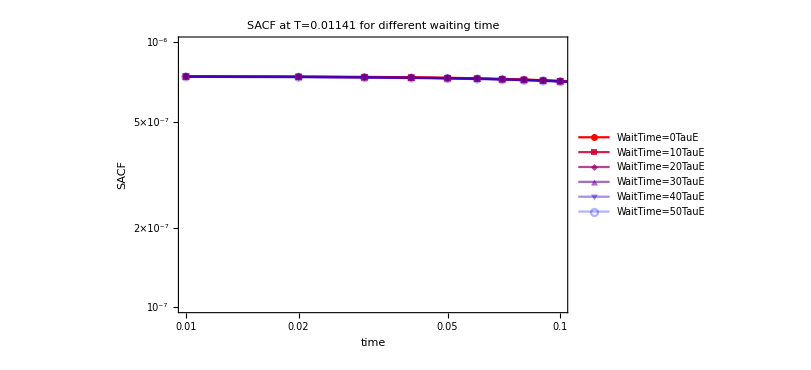

```mathematica
ListLogLogPlot[Table[Table[{Normal[SACtime[[7,wt,1]][[2]]][[t]],Mean[Table[Normal[SACtime[[7,wt,id]][[1]]][[t]],{id,3}]]},{t,Length[Normal[SACtime[[7,wt,1]][[2]]]]}],{wt,6}],PlotStyle->redBluePlotConfig[6],PlotLegends->Table[StringJoin["WaitTime=",ToString[wt],"TauE"],{wt,0,50,10}],FrameLabel->{"time","SACF"},ImageSize->600,PlotLabel->"SACF at T=0.01141 for different waiting time",PlotMarkers->Automatic,Joined->True,PlotRange->{{0.01,0.1},{10^-6,10^-7}}]
```

```mathematica
Normal[SACtime[[7,1,1]][[1]]][[1;;20]]
```

{7.52582×10^-7,7.50794×10^-7,7.48682×10^-7,7.46249×10^-7,7.43503×10^-7,7.40445×10^-7,7.37078×10^-7,7.33408×10^-7,7.29439×10^-7,7.25174×10^-7,7.20618×10^-7,7.1578×10^-7,7.10663×10^-7,7.05278×10^-7,6.99633×10^-7,6.93731×10^-7,6.87524×10^-7,6.74526×10^-7,6.60641×10^-7,6.45944×10^-7}

```mathematica
Normal[SACtime[[7,2,1]][[1]]][[1;;20]]
```

{7.51411×10^-7,7.49629×10^-7,7.47523×10^-7,7.45097×10^-7,7.42358×10^-7,7.39306×10^-7,7.35945×10^-7,7.3228×10^-7,7.28316×10^-7,7.24056×10^-7,7.19507×10^-7,7.14677×10^-7,7.09568×10^-7,7.04192×10^-7,6.98555×10^-7,6.92662×10^-7,6.86463×10^-7,6.73482×10^-7,6.59617×10^-7,6.44941×10^-7}

```mathematica
Normal[SACtime[[7,3,1]][[1]]][[1;;20]]
```

{7.52196×10^-7,7.50414×10^-7,7.48308×10^-7,7.45883×10^-7,7.43144×10^-7,7.40093×10^-7,7.36732×10^-7,7.33068×10^-7,7.29105×10^-7,7.24846×10^-7,7.20298×10^-7,7.15468×10^-7,7.10361×10^-7,7.04985×10^-7,6.99348×10^-7,6.93456×10^-7,6.87258×10^-7,6.74278×10^-7,6.60413×10^-7,6.45739×10^-7}

```mathematica
Normal[SACtime[[7,2,1]][[1]]][[1;;20]]
```

{7.51411×10^-7,7.49629×10^-7,7.47523×10^-7,7.45097×10^-7,7.42358×10^-7,7.39306×10^-7,7.35945×10^-7,7.3228×10^-7,7.28316×10^-7,7.24056×10^-7,7.19507×10^-7,7.14677×10^-7,7.09568×10^-7,7.04192×10^-7,6.98555×10^-7,6.92662×10^-7,6.86463×10^-7,6.73482×10^-7,6.59617×10^-7,6.44941×10^-7}

```mathematica
Normal[SACtime[[7,3,1]][[1]]][[1;;20]]
```

{7.52196×10^-7,7.50414×10^-7,7.48308×10^-7,7.45883×10^-7,7.43144×10^-7,7.40093×10^-7,7.36732×10^-7,7.33068×10^-7,7.29105×10^-7,7.24846×10^-7,7.20298×10^-7,7.15468×10^-7,7.10361×10^-7,7.04985×10^-7,6.99348×10^-7,6.93456×10^-7,6.87258×10^-7,6.74278×10^-7,6.60413×10^-7,6.45739×10^-7}

```mathematica
Normal[SACtime[[7,4,1]][[1]]][[1;;20]]
```

{7.53896×10^-7,7.52112×10^-7,7.50004×10^-7,7.47575×10^-7,7.44831×10^-7,7.41774×10^-7,7.38405×10^-7,7.34732×10^-7,7.30759×10^-7,7.2649×10^-7,7.2193×10^-7,7.17089×10^-7,7.11968×10^-7,7.06579×10^-7,7.00927×10^-7,6.95018×10^-7,6.88803×10^-7,6.75787×10^-7,6.61884×10^-7,6.47168×10^-7}

```mathematica
Normal[SACtime[[7,5,1]][[1]]][[1;;20]]
```

{7.5128×10^-7,7.49497×10^-7,7.4739×10^-7,7.44963×10^-7,7.42222×10^-7,7.39167×10^-7,7.35802×10^-7,7.32132×10^-7,7.28162×10^-7,7.23895×10^-7,7.19339×10^-7,7.14503×10^-7,7.09387×10^-7,7.04005×10^-7,6.98359×10^-7,6.92458×10^-7,6.86252×10^-7,6.73255×10^-7,6.59373×10^-7,6.44682×10^-7}

### SACF at different T

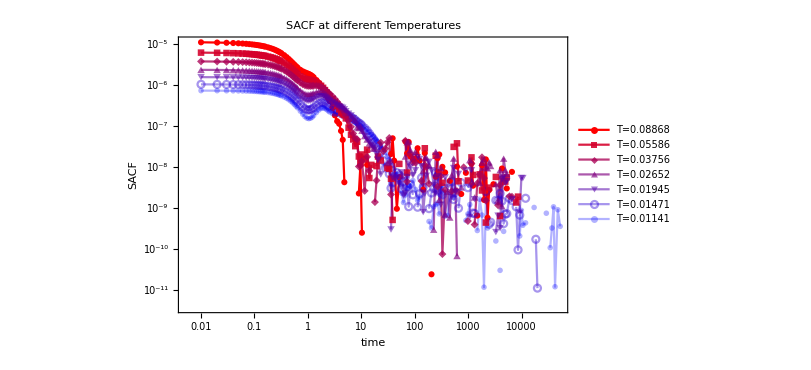

```mathematica
ListLogLogPlot[Table[Table[{Normal[SACtime[[T,6,1]][[2]]][[t]],Mean[Table[Normal[SACtime[[T,6,id]][[1]]][[t]],{id,3}]]},{t,Length[Normal[SACtime[[T,6,1]][[2]]]]}],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[7],PlotLegends->Table[StringJoin["T=",ToString[Tlist[[T]]]],{T,Length[Tlist]}],FrameLabel->{"time","SACF"},ImageSize->600,PlotLabel->"SACF at different Temperatures",PlotMarkers->Automatic,Joined->True]
```

### SACF*β*Area

From Wittmer et. al., G(t)=SACF*β*Area+Geq. Here I plot SACF*β*Area.

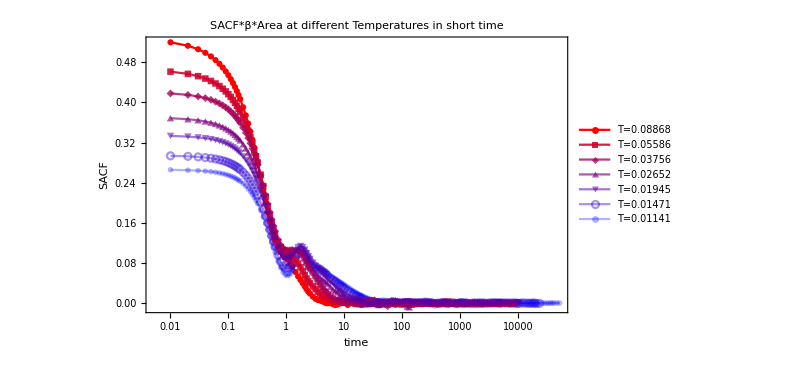

```mathematica
ListLogLinearPlot[Table[Table[{Normal[SACtime[[T,6,1]][[2]]][[t]],Mean[Table[Normal[SACtime[[T,6,id]][[1]]][[t]],{id,3}]]/Tlist[[T]]*4096},{t,Length[Normal[SACtime[[T,6,1]][[2]]]]}],{T,Length[Tlist]}],PlotStyle->redBluePlotConfig[7],PlotLegends->Table[StringJoin["T=",ToString[Tlist[[T]]]],{T,Length[Tlist]}],FrameLabel->{"time","SACF"},ImageSize->600,PlotLabel->"SACF*β*Area at different Temperatures in short time",PlotMarkers->Automatic,Joined->True]
```

## Stress-Fluctuation

Geq=G1-G2

### calculating G1,G2,Geq

```mathematica
G1=Table[Mean[Flatten[Table[Normal[Derivatives[[T,idx]][[2]]][[20000;;]]/4096,{idx,3}]]],{T,Length[Tlist]}]
```

{0.798492,0.647996,0.536087,0.451723,0.386549,0.335389,0.294428}

```mathematica
G2=Table[Variance[Flatten[Table[Normal[Derivatives[[T,idx]][[1]]][[20000;;]]*4096,{idx,3}]]]/Tlist[[T]]/4096,{T,Length[Tlist]}]
```

{0.525639,0.467774,0.419708,0.368727,0.335919,0.294983,0.265258}

```mathematica
Geq=G1-G2
```

{0.272854,0.180222,0.116379,0.0829965,0.0506294,0.0404058,0.0291694}

```mathematica
Geqfit=NonlinearModelFit[Geq,a Exp[b T],{a,b,c},T]
```

FittedModel[0.405833 ⅇ^(-0.403303 T)]

### Geq vs T

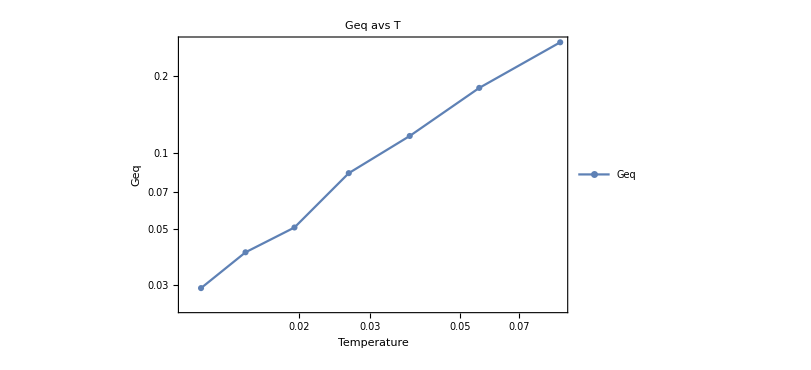

```mathematica
Geqplot=ListLogLogPlot[Table[{Tlist[[T]],Geq[[T]]},{T,Length[Tlist]}],FrameLabel->{"Temperature","Geq"},ImageSize->600,PlotLabel->"Geq avs T",PlotMarkers->Automatic,Joined->True,PlotLegends->{"Geq"}]
```

```mathematica
Show[Geqplot,LogLogPlot[Geqfit[T],{T,Min[Tlist],Max[Tlist]}]]
```

-Graphics-

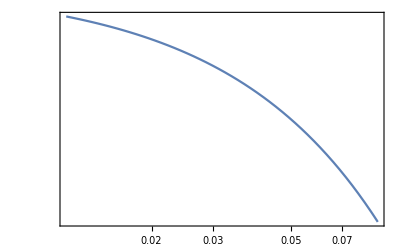

```mathematica
LogLogPlot[Geqfit[T],{T,Min[Tlist],Max[Tlist]}]
```

### G1 vs T

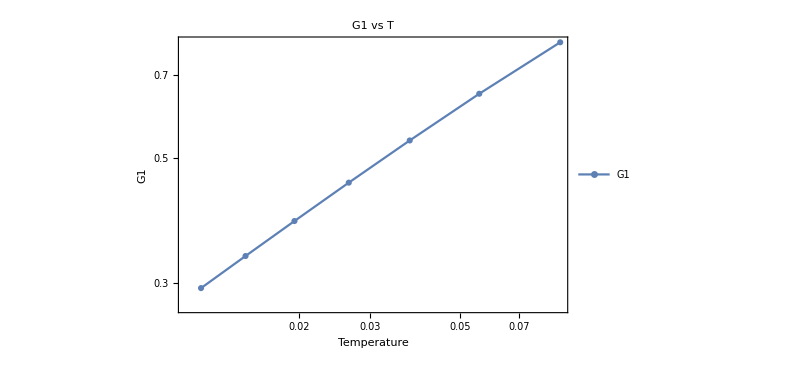

```mathematica
G1plot=ListLogLogPlot[Table[{Tlist[[T]],G1[[T]]},{T,Length[Tlist]}],FrameLabel->{"Temperature","G1"},ImageSize->600,PlotLabel->"G1 vs T",PlotMarkers->Automatic,Joined->True,PlotLegends->{"G1"}]
```

### G1 and Geq vs T

```mathematica
G1plotZoomed=ListLogLogPlot[Table[{Tlist[[T]],G1[[T]]},{T,Length[Tlist]}],FrameLabel->{"Temperature","G"},ImageSize->600,PlotLabel->"G1 and Geq vs T",PlotStyle->redBluePlotConfig[2][[1]],PlotMarkers->Automatic,Joined->True,PlotRange->{Automatic,{0.02,0.9}},PlotLegends->{"G1"}];
```

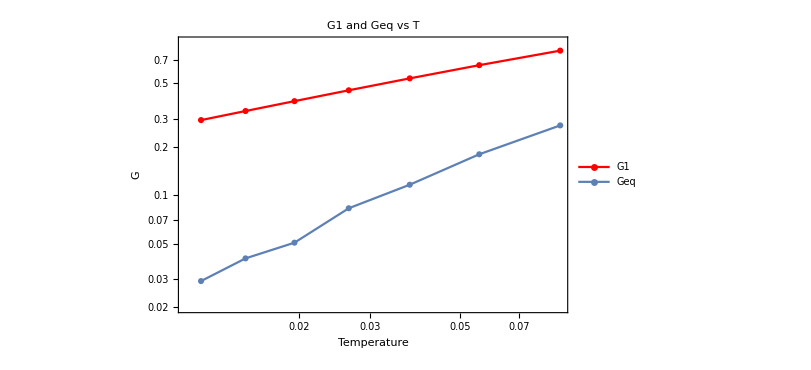

```mathematica
Show[G1plotZoomed,Geqplot]
```

### G(t=0) and G1

Because G(t)=SACF*β*Area+Geq, G(t=0)=SACF(t=0)*β*Area+Geq. G(t=0) should be equal to G1. Let’s verify it!

```mathematica
GTshortTimeplot=ListLogLogPlot[Table[{Tlist[[T]],Mean[Table[Normal[SACtime[[T,6,id]][[1]]][[1]],{id,3}]]/Tlist[[T]]*4096+Geq[[T]]},{T,Length[Tlist]}],FrameLabel->{"Temperature","G"},ImageSize->600,PlotStyle->redBluePlotConfig[10][[1]],PlotLabel->"G(t=0) and G1 vs T",PlotMarkers->Automatic,Joined->True,PlotLegends->{"G(t=0)"}];
```

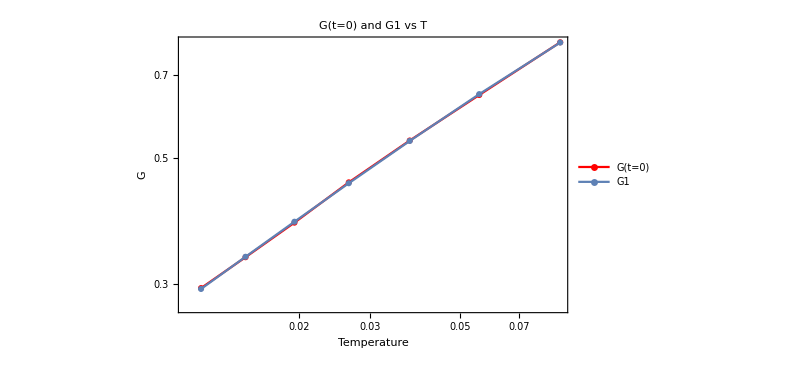

```mathematica
Show[GTshortTimeplot,G1plot]
```